```mathematica
α=2;
β=2;
γ=2;
ζ=2;
Subscript[h, 0]=0;
Subscript[h, 1]=2;
Subscript[h, 2]=4;
Subscript[h, 3]=6;
```

```mathematica
(*Caso discontinuidad en x=Subscript[h, 0]*)Subscript[A, 0]={{Exp[k Subscript[h, 0]], Exp[-k Subscript[h, 0]]},{k Exp[k Subscript[h, 0]], -k Exp[-k Subscript[h, 0]]}};(*matriz Subscript[A, 0]*)
Subscript[CA, 0]={{1,0},{- α,1}};(*matriz de condiciones de frontera*)
Subscript[CD, 00]={{Subscript[c, 0]},{0}};(*Matriz semilla*)
Subscript[A, 00]=Inverse[Subscript[A, 0]] . Subscript[CA, 0] . Subscript[A, 0] ;(*Matriz Subscript[M, 0]*)
```

```mathematica
(*Subscript[A, 00][[1,1]]
Subscript[A, 00][[2,1]]*)
```

(1-1/k) c_0

c_0/k

```mathematica
(*Caso discontinuidad en x=Subscript[h, 1]*)Subscript[A, 1]={{Exp[k Subscript[h, 1]], Exp[-k Subscript[h, 1]]},{k Exp[k Subscript[h, 1]], -k Exp[-k Subscript[h, 1]]}};(*matriz Subscript[A, 0]*)
Subscript[CA, 1]={{1,0},{-β,1}};(*matriz de condiciones de frontera*)
Subscript[A, 11]=Inverse[Subscript[A, 1]] . Subscript[CA, 1] . Subscript[A, 1] ;(*Matriz Subscript[M, 0]*)
(*Subscript[A, 11][[1,1]]//Simplify
Subscript[A, 11][[2,1]]//Simplify*)
```

```mathematica
(*Caso discontinuidad en x=Subscript[h, 2]*)Subscript[A, 2]={{Exp[k Subscript[h, 2]], Exp[-k Subscript[h, 2]]},{k Exp[k Subscript[h, 2]], -k Exp[-k Subscript[h, 2]]}};(*matriz Subscript[A, 0]*)
Subscript[CA, 2]={{1,0},{-γ,1}};(*matriz de condiciones de frontera*)
Subscript[A, 22]=Inverse[Subscript[A, 2]] . Subscript[CA, 2] . Subscript[A, 2] ;(*Matriz Subscript[M, 0]*)
```

```mathematica
(*Subscript[A, 22][[1,1]]//Simplify
Subscript[A, 22][[2,1]]//Simplify*)
```

```mathematica
(*Caso discontinuidad en x=Subscript[h, 3]*)Subscript[A, 3]={{Exp[k Subscript[h, 3]], Exp[-k Subscript[h, 3]]},{k Exp[k Subscript[h, 3]], -k Exp[-k Subscript[h, 3]]}};(*matriz Subscript[A, 3]*)
Subscript[CA, 3]={{1,0},{-ζ,1}};(*matriz de condiciones de frontera*)
Subscript[A, 33]=Inverse[Subscript[A, 3]] . Subscript[CA, 3] . Subscript[A, 3] . Subscript[A, 22] . Subscript[A, 11] . Subscript[A, 00] . Subscript[CD, 00] ;(*Matriz Subscript[M, 0]*)
```

```mathematica
Subscript[A, 33][[1,1]]//Simplify
Subscript[A, 33][[2,1]]//Simplify
```

(ⅇ^(-12 k) (-3 ⅇ^(8 k) (-1+k)^2+ⅇ^(12 k) (-1+k)^4-(1+k)^2+ⅇ^(4 k) (3-2 k^2)) c_0)/k^4

((ⅇ^(12 k) (-1+k)^3+(1+k)^3+ⅇ^(8 k) (3-3 k-k^2+k^3)+ⅇ^(4 k) (-3-3 k+k^2+k^3)) c_0)/k^4

```mathematica
κ[k_]:=1/k^4 ⅇ^(-12 k) (-3 ⅇ^(8 k) (-1+k)^2+ⅇ^(12 k) (-1+k)^4-(1+k)^2+ⅇ^(4 k) (3-2 k^2)) Subscript[c, 0];(*Define la ecuación de dispersión*)
NSolve[κ[k]==0,k,Reals](*Obtiene eigen-valores*)
```

{{k→-1.08093},{k→0.866081},{k→1.16592},{k→-0.681145},{k→0.542881},{k→1.06016}}

```mathematica
kj={1.165919394730377,1.0601637993793238,0.8660810903898355,0.5428814676421063};(*Arreglo de k permitidos*)
ϕj[x_,n_]:=Piecewise[{{Exp[kj[[n]]x] ,x<0},{(1-1/kj[[n]])  Exp[kj[[n]]x]+(1/kj[[n]])Exp[-kj[[n]]x] ,0<x<Subscript[h, 1]},{((ⅇ^(-4 kj[[n]])(-1+ⅇ^(4 kj[[n]]) (-1+kj[[n]])^2))/(kj[[n]])^2 ) Exp[kj[[n]]x]+((1+ⅇ^(4 kj[[n]]) (-1+kj[[n]])+kj[[n]]) /(kj[[n]])^2)Exp[-kj[[n]]x] ,Subscript[h, 1]<x<Subscript[h, 2]},{(1/(kj[[n]])^3 ⅇ^(-8 kj[[n]]) (-1-2 ⅇ^(4 kj[[n]]) (-1+kj[[n]])+ⅇ^(8 kj[[n]]) (-1+kj[[n]])^3-kj[[n]]))Exp[kj[[n]]x] +(1/(kj[[n]])^3(ⅇ^(8 kj[[n]]) (-1+kj[[n]])^2+(1+kj[[n]])^2+ⅇ^(4 kj[[n]]) (-2+(kj[[n]])^2)) )Exp[-kj[[n]]x],Subscript[h, 2]<x<Subscript[h, 3]},{(1/(kj[[n]])^4(ⅇ^(12 kj[[n]]) (-1+kj[[n]])^3+(1+kj[[n]])^3+ⅇ^(8 kj[[n]]) (3-3 kj[[n]]-(kj[[n]])^2+(kj[[n]])^3)+ⅇ^(4 kj[[n]]) (-3-3 kj[[n]]+(kj[[n]])^2+(kj[[n]])^3)))Exp[-kj[[n]]x],x>Subscript[h, 3]}}];
(*Definición de la eigen-función*)
```

```mathematica
Mj[n_]:=√(∫_(-∞)^0 (Abs[ϕj[x,n]])^2 ⅆx+∫_0^Subscript[h, 1] (Abs[ϕj[x,n]])^2 ⅆx+∫_Subscript[h, 1]^Subscript[h, 2] (Abs[ϕj[x,n]])^2 ⅆx+∫_Subscript[h, 2]^Subscript[h, 3] (Abs[ϕj[x,n]])^2 ⅆx+∫_Subscript[h, 3]^∞ (Abs[ϕj[x,n]])^2 ⅆx);(*Define las constantes de normalización*)
Mj[1]
Mj[2]
Mj[3]
Mj[4]
(*Obtenemos el elemento correspondiente para generar el arreglo de constantes de normalización*)
```

2.59811

1.61433

1.63204

2.71459

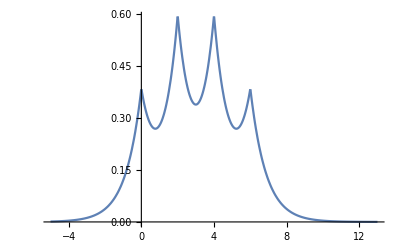

```mathematica
M={2.5981060586199236,1.6143321603918634,1.6320360970121266,2.7145886543905395};(*Constantes de normalización de cada eigen-función*)
Plot[1/M[[1]] ϕj[x,1],{x,-5,13},PlotRange->All](*Gráfica de la eigen-función*)
```

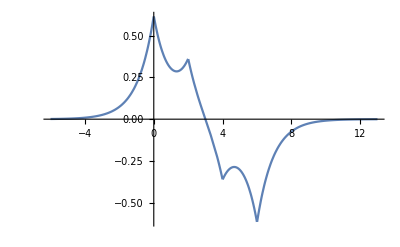

```mathematica
Plot[1/M[[2]] ϕj[x,2],{x,-6,13},PlotRange->All]
```

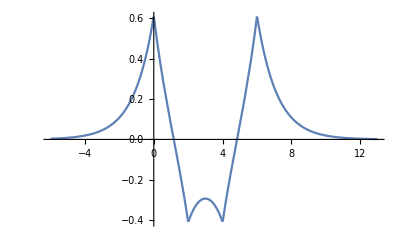

```mathematica
Plot[1/M[[3]] ϕj[x,3],{x,-6,13},PlotRange->All]
```

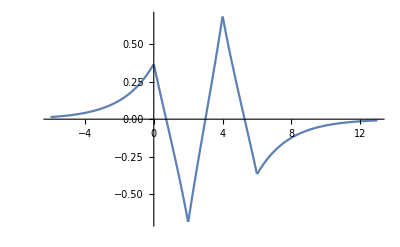

```mathematica
Plot[1/M[[4]] ϕj[x,4],{x,-6,13},PlotRange->All]
```

```mathematica
(1/k^3 ⅇ^(-8 k) (-1-2 ⅇ^(4 k) (-1+k)+ⅇ^(8 k) (-1+k)^3-k))Exp[k x] +(1/k^3(ⅇ^(8 k) (-1+k)^2+(1+k)^2+ⅇ^(4 k) (-2+k^2)) )Exp[-k x]//Simplify
```

1/k^3 ⅇ^(-k x) (ⅇ^(2 k (-4+x)) (-1-2 ⅇ^(4 k) (-1+k)+ⅇ^(8 k) (-1+k)^3-k)+ⅇ^(8 k) (-1+k)^2+(1+k)^2+ⅇ^(4 k) (-2+k^2))

```mathematica
(1/k^4(ⅇ^(12 k) (-1+k)^3+(1+k)^3+ⅇ^(8 k) (3-3 k-k^2+k^3)+ⅇ^(4 k) (-3-3 k+k^2+k^3)))Exp[-k x]//Simplify
```

1/k^4 ⅇ^(-k x) (ⅇ^(12 k) (-1+k)^3+(1+k)^3+ⅇ^(8 k) (3-3 k-k^2+k^3)+ⅇ^(4 k) (-3-3 k+k^2+k^3))